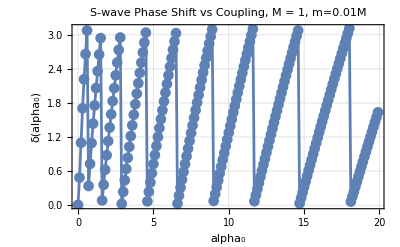

```mathematica
(*---PARAMETERS---*)
M=1;                (* Mass of Nucleon*)
m=0.1*M;               (*Pion mass*)
k0=m;    (*Momentum*)
E0=k0^2/M;              (*Energy*)
r0=10^-6;          (*Small value near r=0 for boundary condition*)

αMin = 0.001;
αMax = 20; 
αSpacing = 0.1;
λ = 2*Pi/Abs[k0]; (* De Broglie Wavelength*)
rMax=20*λ;           (*Max radius for numerical integration, ensures asymptotic behavior by being much larger than λ*)
fitStart=0.8*rMax;       (*Start of asymptotic region*)
fitEnd=rMax;         (*End of asymptotic region*)
fitSpacing = rMax/100;    (* Interval spacing in asymptotic region*)

(*---Phase Shift Extractor---*)
ClearAll[extractPhaseShift]

extractPhaseShift[a0_?Positive,M_?Positive]:=Module[{k,sol,uFunc,data,fit,δ},k=Sqrt[M*E0];
(*---Yukawa Potential---*)
V[r_]:=-a0*Exp[-m*r]/r;
(*Numerical solution to Schrödinger equation*)
sol=NDSolve[{u''[r]==M*(V[r]-E0) u[r],u[r0]==r0,u'[r0]==1},u,{r,r0,rMax},MaxSteps->Infinity];
(*Wavefunction interpolator*)uFunc=Function[r,Evaluate[u[r]/. sol[[1]]]];
(*Sample numerical wavefunction in asymptotic region*)data=Table[{r,uFunc[r]},{r,fitStart,fitEnd,fitSpacing}];
(*Fit to A*Sin[k*r+δ] to extract phase shift*)fit=NonlinearModelFit[data,A*Sin[k*r+δ],{{A,1},{δ,0}},r];
(*Return δ modulo π (optional,depending on context)*)Mod[δ/. fit["BestFitParameters"],Pi]]

(*---Phase Shift Curve Generator---*)
a0Range=Range[αMin,αMax,αSpacing];  (*Coupling constants to test*)

phaseShiftData=Table[{a0,extractPhaseShift[a0,M]},{a0,a0Range}];

(*---Plot the phase shift vs energy---*)
ListLinePlot[phaseShiftData,PlotMarkers->Automatic,AxesLabel->{"alpha₀","δ(alpha₀)"},PlotLabel->Row[{"S-wave Phase Shift vs Coupling, M = ",M,", m=0.01M"}],Frame->True,GridLines->Automatic,PlotTheme->"Detailed"]
```